```mathematica
ChromialReduce[g_]:=Block[{edges=EdgeList[g], firstEdge, del, contr},
If[Length[edges]≤0,
"["<>ToString[Length[VertexList[g]]]<>"]",
firstEdge=First[edges];
del=EdgeDelete[g,firstEdge];
contr=EdgeContract[g,firstEdge];
Print[del-contr];
ChromialReduce[del]
-
ChromialReduce[contr]

]
]
```

```mathematica
ChromialReduce[g_]:=Block[{edges=EdgeList[g], firstEdge},
If[Length[edges]≤0,
"["<>ToString[StringRiffle[ Sort[VertexList[g],Greater],"*"]]<>"]",
firstEdge=First[edges];
ChromialReduce[EdgeDelete[g,firstEdge]]
-
ChromialReduce[EdgeContract[g,firstEdge]]

]
]
```

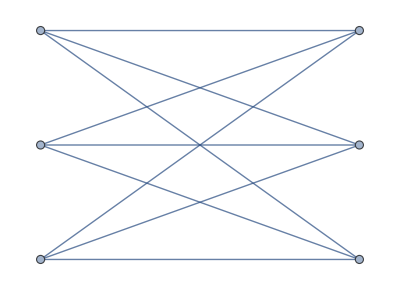

```mathematica
CompleteGraph[{3,3}]
```

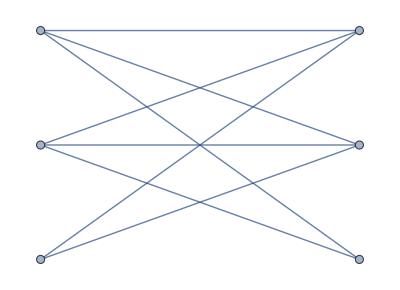
-+-Graphics-

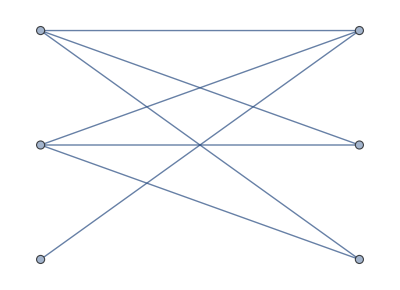
-+-Graphics-

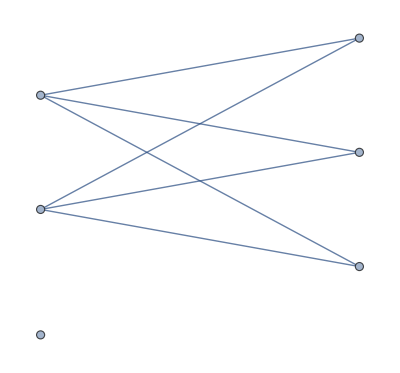
-+-Graphics-

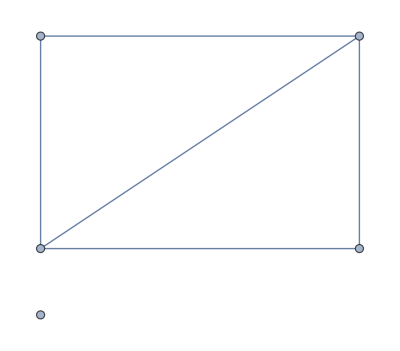
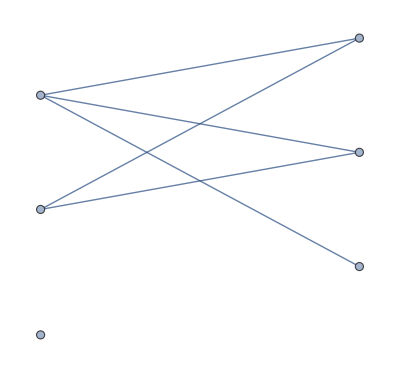
--Graphics-+-Graphics-

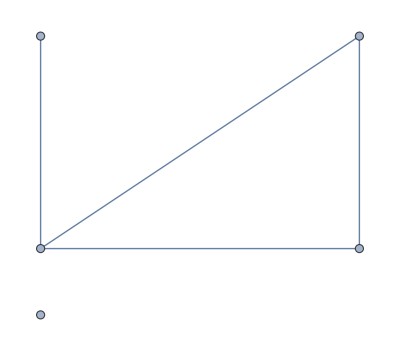
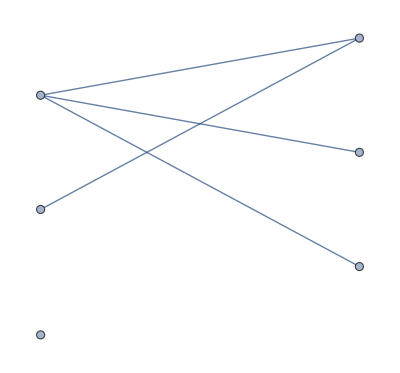
--Graphics-+-Graphics-

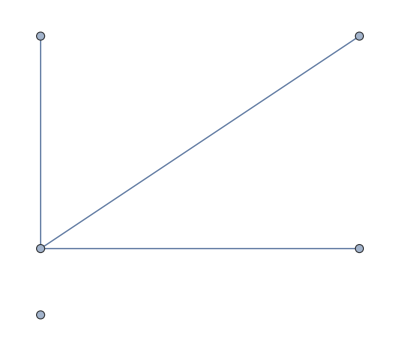
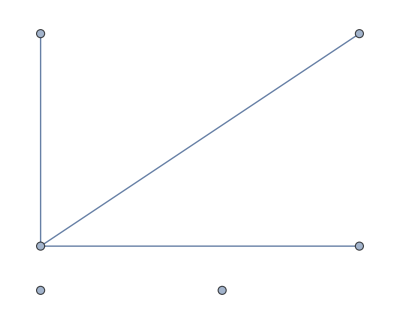
--Graphics-+-Graphics-

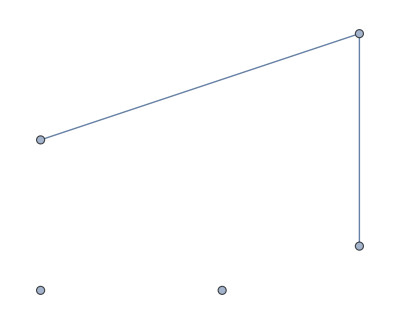
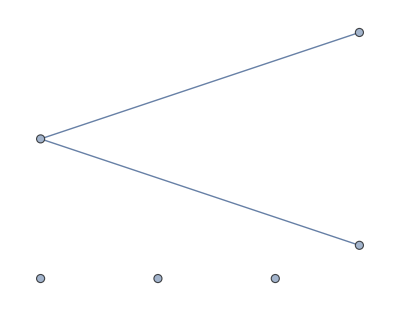
--Graphics-+-Graphics-

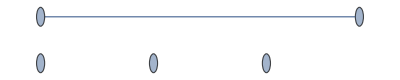
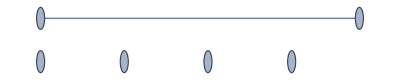
--Graphics-+-Graphics-

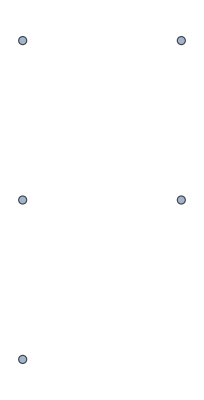
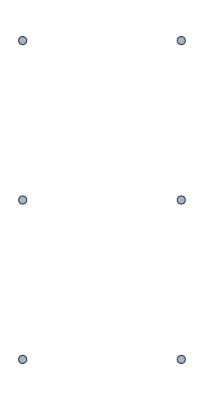
--Graphics-+-Graphics-

--Graphics-+-Graphics-

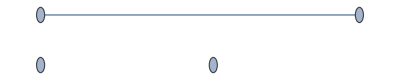
--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

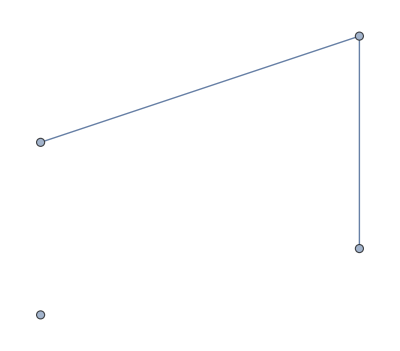
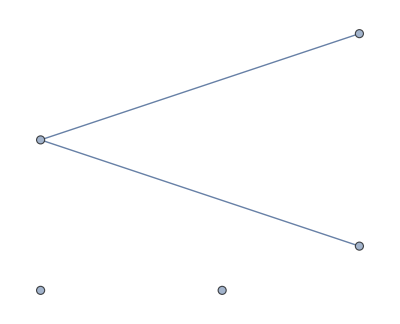
--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

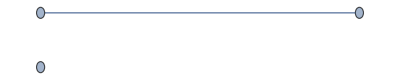
--Graphics-+-Graphics-

--Graphics-+-Graphics-

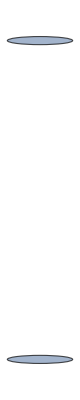
--Graphics-+-Graphics-

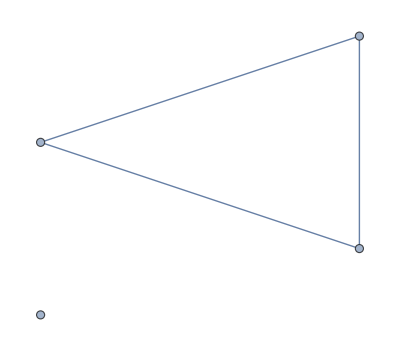
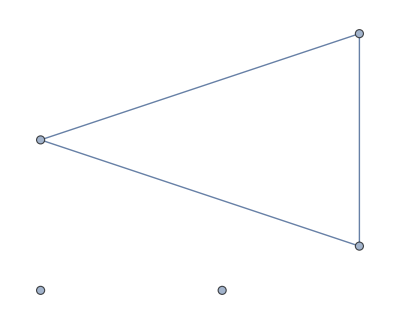
--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

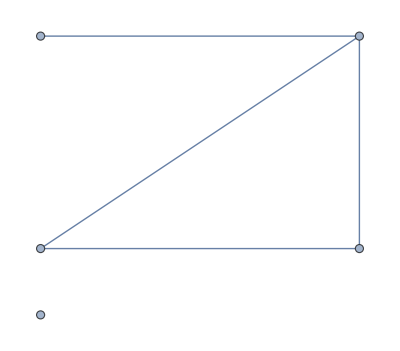
--Graphics-+-Graphics-

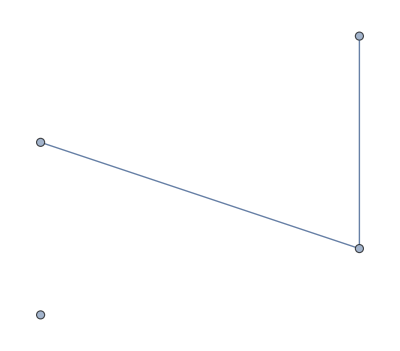
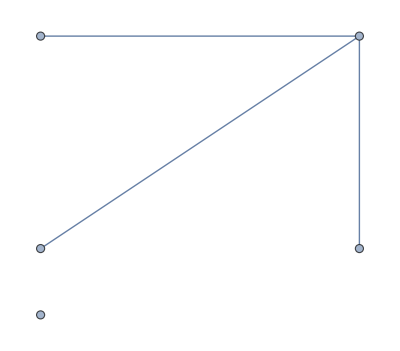
--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

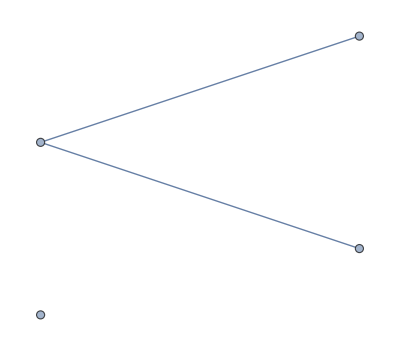
-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-


--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«8 more identical outputs»

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«2 more identical outputs»

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«2 more identical outputs»

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«2 more identical outputs»

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«14 more identical outputs»

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

«2 more identical outputs»

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-+

-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

--Graphics-+-Graphics-

-31 [1]+78 [2]-75 [3]+36 [4]-9 [5]+[6]

```mathematica
ChromialReduce[CompleteGraph[{3,3}]]
```

```mathematica
ChromialReduce[CompleteGraph[5]]
```

24 [1]-50 [2]+35 [3]-10 [4]+[5]